## Линейный конгруэнтный генератор

```mathematica
nMax=100;
mod = 2^8;
lkp[x_,a_,c_,m_]:=RecurrenceTable[{X[n+1]==Mod[(a*X[n]+c),m],X[1]==x},X,{n,1,nMax}];t = Table[{ListPlot[lkp[0,a,c,mod]], a,c}, {a,3,30,3},{c,1,20,3}];

lkp[0,3,1,mod]
```

{0,1,4,13,40,121,108,69,208,113,84,253,248,233,188,53,160,225,164,237,200,89,12,37,112,81,244,221,152,201,92,21,64,193,68,205,104,57,172,5,16,49,148,189,56,169,252,245,224,161,228,173,8,25,76,229,176,17,52,157,216,137,156,213,128,129,132,141,168,249,236,197,80,241,212,125,120,105,60,181,32,97,36,109,72,217,140,165,240,209,116,93,24,73,220,149,192,65,196,77}

### Графики последовательностей с разными начальным значением

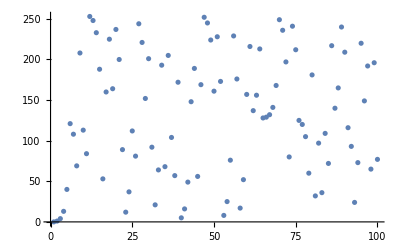
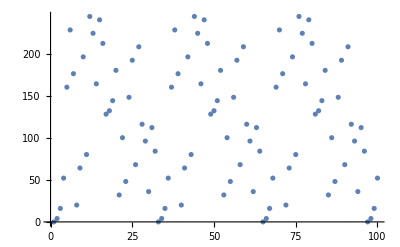
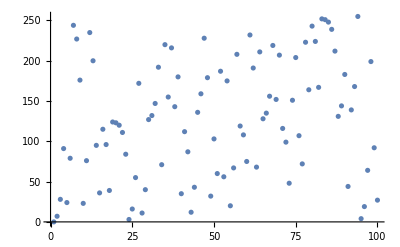
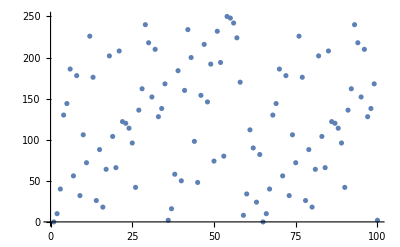
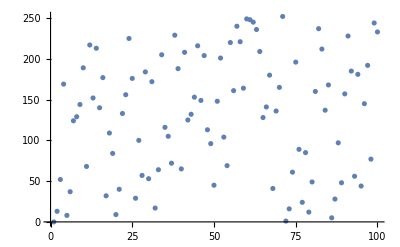
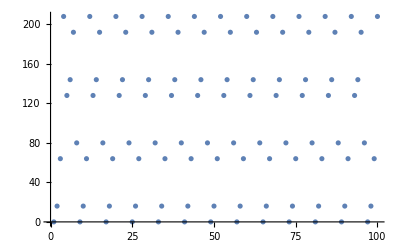
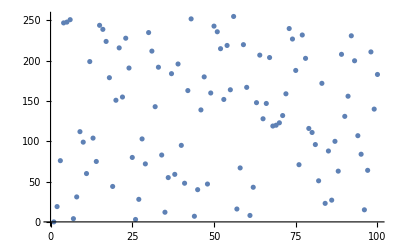
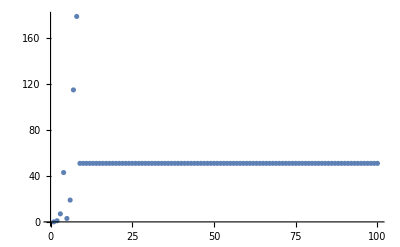
-Graphics-
3
1 | -Graphics-
3
4 | -Graphics-
3
7 | -Graphics-
3
10 | -Graphics-
3
13 | -Graphics-
3
16 | -Graphics-
3
19
-Graphics-
6
1 | -Graphics-
6
4 | -Graphics-
6
7 | -Graphics-
6
10 | -Graphics-
6
13 | -Graphics-
6
16 | -Graphics-
6
19
-Graphics-
9
1 | -Graphics-
9
4 | -Graphics-
9
7 | -Graphics-
9
10 | -Graphics-
9
13 | -Graphics-
9
16 | -Graphics-
9
19
-Graphics-
12
1 | -Graphics-
12
4 | -Graphics-
12
7 | -Graphics-
12
10 | -Graphics-
12
13 | -Graphics-
12
16 | -Graphics-
12
19
-Graphics-
15
1 | -Graphics-
15
4 | -Graphics-
15
7 | -Graphics-
15
10 | -Graphics-
15
13 | -Graphics-
15
16 | -Graphics-
15
19
-Graphics-
18
1 | -Graphics-
18
4 | -Graphics-
18
7 | -Graphics-
18
10 | -Graphics-
18
13 | -Graphics-
18
16 | -Graphics-
18
19
-Graphics-
21
1 | -Graphics-
21
4 | -Graphics-
21
7 | -Graphics-
21
10 | -Graphics-
21
13 | -Graphics-
21
16 | -Graphics-
21
19
-Graphics-
24
1 | -Graphics-
24
4 | -Graphics-
24
7 | -Graphics-
24
10 | -Graphics-
24
13 | -Graphics-
24
16 | -Graphics-
24
19
-Graphics-
27
1 | -Graphics-
27
4 | -Graphics-
27
7 | -Graphics-
27
10 | -Graphics-
27
13 | -Graphics-
27
16 | -Graphics-
27
19
-Graphics-
30
1 | -Graphics-
30
4 | -Graphics-
30
7 | -Graphics-
30
10 | -Graphics-
30
13 | -Graphics-
30
16 | -Graphics-
30
19

```mathematica
TableForm[t]
```